FittedModel[-32.1378+0.63584 T]

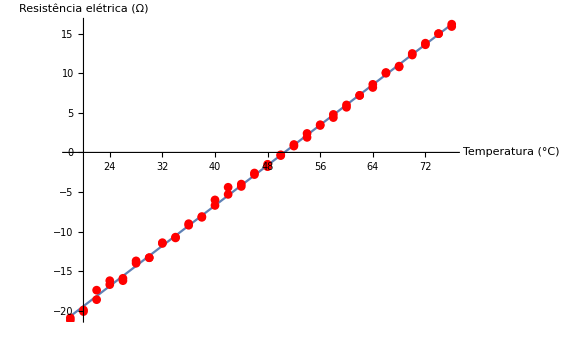

```mathematica
data={{18,-20.9,-21.2},{20,-19.9,-20.1},{22,-17.4,-18.6},{24,-16.2,-16.7},{26,-15.9,-16.2},{28,-14,-13.7},{30,-13.3,-13.3},{32,-11.5,-11.4},{34,-10.7,-10.8},{36,-9.2,-9},{38,-8.1,-8.2},{40,-6,-6.7},{42,-5.3,-4.4},{44,-4.3,-4},{46,-2.8,-2.6},{48,-1.5,-1.8},{50,-0.4,-0.3},{52,1,0.8},{54,2.4,1.9},{56,3.4,3.5},{58,4.4,4.8},{60,5.7,6},{62,7.2,7.2},{64,8.2,8.6},{66,10,10.1},{68,10.8,10.9},{70,12.5,12.3},{72,13.6,13.8},{74,15,15},{76,16.2,15.9}};
separated=Join[data[[All, {1, 2}]], data[[All, {1, 3}]]];

model=LinearModelFit[separated, T, T]

plot=Show[
Plot[model[T], {T, Min[data[[All, 1]]], Max[data[[All, 1]]]}],
ListPlot[separated, PlotStyle->{Red}],
AxesLabel->{"Temperatura (°C)", "Resistência elétrica (Ω)"}
]
Export[NotebookDirectory[]<>"Images/Pt100-Experimental.pdf", plot];


data={{18,-20.9,-21.2},{20,-19.9,-20.1},{22,-17.4,-18.6},{24,-16.2,-16.7},{26,-15.9,-16.2},{28,-14,-13.7},{30,-13.3,-13.3},{32,-11.5,-11.4},{34,-10.7,-10.8},{36,-9.2,-9},{38,-8.1,-8.2},{40,-6,-6.7},{42,-5.3,-4.4},{44,-4.3,-4},{46,-2.8,-2.6},{48,-1.5,-1.8},{50,-0.4,-0.3},{52,1,0.8},{54,2.4,1.9},{56,3.4,3.5},{58,4.4,4.8},{60,5.7,6},{62,7.2,7.2},{64,8.2,8.6},{66,10,10.1},{68,10.8,10.9},{70,12.5,12.3},{72,13.6,13.8},{74,15,15},{76,16.2,15.9}};
separated=Join[data[[All, {1, 2}]], data[[All, {1, 3}]]];

model=LinearModelFit[separated, T, T]

plot=Show[
Plot[model[T], {T, Min[data[[All, 1]]], Max[data[[All, 1]]]}],
ListPlot[separated, PlotStyle->{Red}],
AxesLabel->{"Temperatura (°C)", "Resistência elétrica (mV)"}
]
Export[NotebookDirectory[]<>"Images/Pt100-Experimental-Bridge.pdf", plot];

Export[NotebookFileName[EvaluationNotebook[]]<>".pdf", EvaluationNotebook[]];
```